```mathematica
Quit
```

```mathematica
NotebookDirectory[]
```

/Users/esser/Documents/PROJECTS/ALPsPheno/ALP GLOBAL/github/ALP_Global/notebooks/

## Fit the cross section as a polynomial in C_B and C_W

```mathematica
(* list (CB, CW, sigma)*)
VBFsigma = {{-1,1, 0.02754},{0,1,0.005774},{1,1,0.005672 }, {-1,-1, 0.005566}, {0,-1,0.00579 },{1,-1,0.02753}, {-1,0, 0.001014}, {0,0,0}, {1,0, 0.001018}, {0,2,0.09295}, {0.5, 1, 0.003394},{-0.5, 1, 0.01313}, {1,0.5,0.001871}, {1,-0.5,0.005791},{-0.1,0.1, 2.754*10^-06}};
```

```mathematica
Fit[VBFsigma,{CB^4,CB^3 *CW, CB^2*CW^2, CB*CW^3, CW^4},{CB,CW}]
```

0.00102865 CB^4-0.00160019 CB^3 CW+0.00973456 CB^2 CW^2-0.00935486 CB CW^3+0.00580889 CW^4

```mathematica
sigmaVBF[CB_,CW_]:=0.0010286470032311028 CB^4-0.0016001897983539096 CB^3 CW+0.009734562945808179 CB^2 CW^2-0.009354856465020562 CB CW^3+0.0058088939579702915 CW^4
```

```mathematica
sigmaVBF[-0.1,0.1]
```

2.75272×10^-6

```mathematica
Fit[VBFsigma,{CB^4, CB^2*CW^2, CW^4},{CB,CW}]
```

0.00102865 CB^4+0.00973456 CB^2 CW^2+0.00580889 CW^4

```mathematica
sigmaVBFnoCross[CB_,CW_]:=0.0010286470009428926 CB^4+0.009734562974059667 CB^2 CW^2+0.005808893957937185 CW^4
```

```mathematica
sigmaVBFnoCross[0.1,0.1]
```

1.65721×10^-6

## pT of the photon for γZjj

```mathematica
data ={5.9000*10^-02,2.6400*10^-02,7.4000*10^-03,1.4700*10^-03};
```

```mathematica
dataUnc = {2.1000*10^-02,6.0000*10^-03,2.4000*10^-03,6.8000*10^-04};
```

```mathematica
background ={5.3900*10^-02,1.3400*10^-02,4.9000*10^-03,1.1400*10^-03};
```

```mathematica
signal0={4.3539*10^-04,8.1827*10^-04,1.0735*10^-03,1.1049*10^-03};
```

```mathematica
binCenter={50,100,160,300};
```

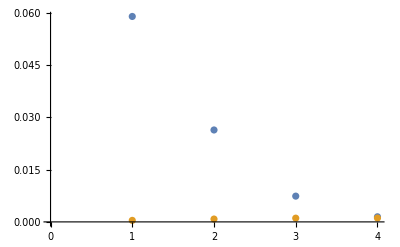

```mathematica
ListPlot[{data,signal0}]
```

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
Nevents[CB_, CW_]:=background+signal0*sigmaVBF[CB,CW]/sigmaVBF[0,1];
```

```mathematica
chi2[CB_, CW_]:=Sum[((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2,{i,0,Length[data]}];
```

```mathematica
chi2[0,1]
```

5.82329

```mathematica
chi2min=FindMinimum[chi2[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{6.074,{CB→0.,CW→0.}}

```mathematica
chi2bin= Table[(((data[[i]]-Nevents[CB,CW][[i]])/dataUnc[[i]])^2-chi2min[[1]]/Length[data])/(chi2[CB,CW]-chi2min[[1]]),{i,1,Length[data]}];
```

```mathematica
Length[chi2bin]
```

4

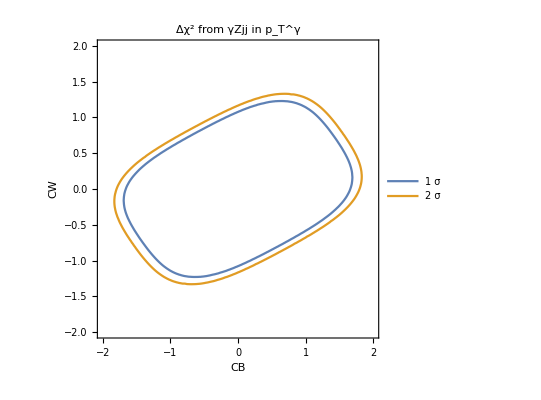

```mathematica
chi2PlotZgammajjpTgamma = ContourPlot[{chi2[CB,CW]-chi2min[[1]]==1,chi2[CB,CW]-chi2min[[1]]==4},{CB,-2,2},{CW,-2,2} ,FrameLabel->(Style[#,14,Bold]&/@{CB,CW}),PlotLegends->{"1 σ", "2 σ"}, PlotLabel->"Δχ^2 from γZjj in p_T^γ"]
```

```mathematica
Export["../Figures/chi2_Zgammajj_pTgamma.pdf",chi2PlotZgammajjpTgamma];
```

```mathematica
chi2[0,-1.10]
```

7.64975

```mathematica
Solve[chi2[0,CW]-chi2min[[1]]==4,CW]
```

{{CW→-1.16557},{CW→-0.65978-0.65978 ⅈ},{CW→-0.65978+0.65978 ⅈ},{CW→0.-1.16557 ⅈ},{CW→0.+1.16557 ⅈ},{CW→0.65978-0.65978 ⅈ},{CW→0.65978+0.65978 ⅈ},{CW→1.16557}}

```mathematica
Solve[chi2[CB,0]-chi2min[[1]]==4,CB]
```

{{CB→-1.79678},{CB→-1.01708-1.01708 ⅈ},{CB→-1.01708+1.01708 ⅈ},{CB→0.-1.79678 ⅈ},{CB→0.+1.79678 ⅈ},{CB→1.01708-1.01708 ⅈ},{CB→1.01708+1.01708 ⅈ},{CB→1.79678}}

The individual 2σ limits are CW=1.17 and CB=1.80 for the respective other WC zero.

Plot the χ^2 per bin minus the averaged χ^2per bin (i.e. χ^2/number of bins) and normalise by the total χ^2-(χ^2)_min:

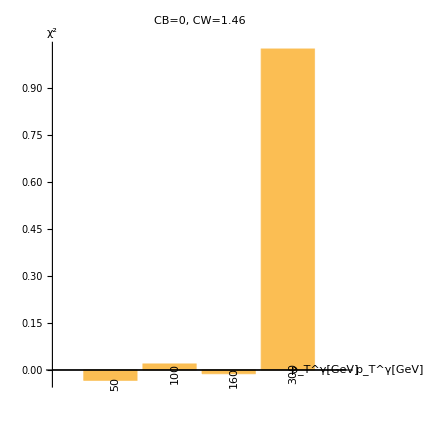

```mathematica
BarChart[chi2bin/.{CB->0, CW->1.46},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=1.46",AspectRatio->1]
```

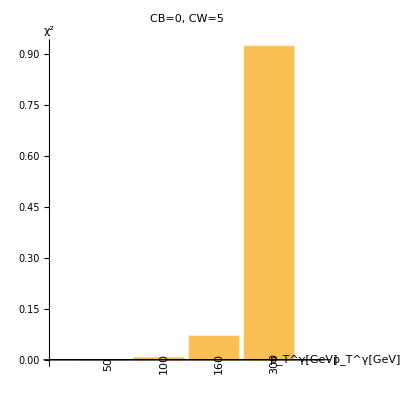

```mathematica
BarChart[chi2bin/.{CB->0, CW->5},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=5",AspectRatio->1]
```

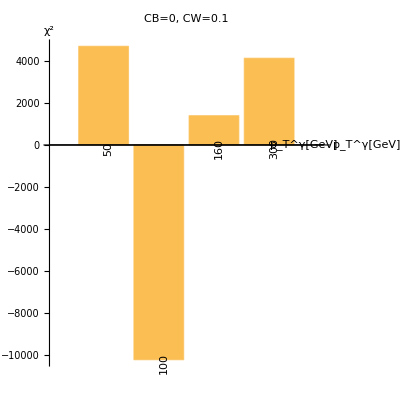

```mathematica
BarChart[chi2bin/.{CB->0, CW->0.1},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0, CW=0.1",AspectRatio->1]
```

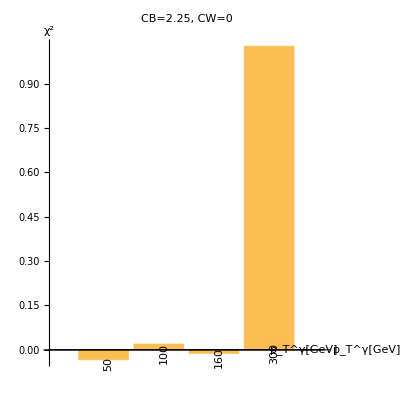

```mathematica
BarChart[chi2bin/.{CB->2.25, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=2.25, CW=0",AspectRatio->1]
```

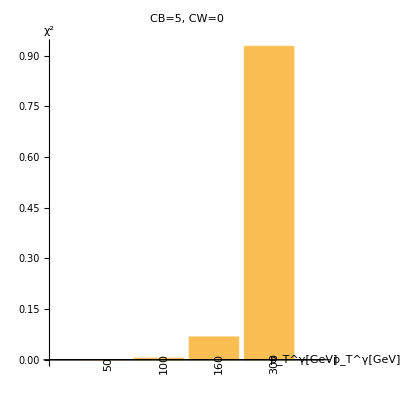

```mathematica
BarChart[chi2bin/.{CB->5, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=5, CW=0",AspectRatio->1]
```

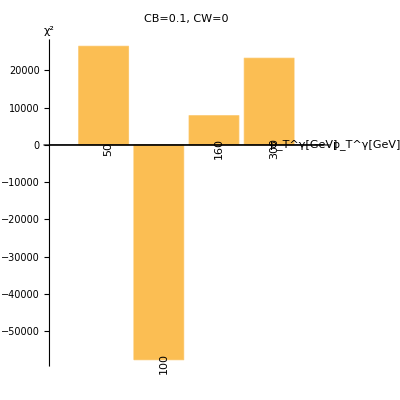

```mathematica
BarChart[chi2bin/.{CB->0.1, CW->0},ChartLabels->Placed[binCenter,Below,Rotate[#,90 Degree]&], AxesLabel->{"p_T^γ[GeV]", "χ^2"},PlotLabel->"CB=0.1, CW=0",AspectRatio->1]
```

## pT of the leading jet

```mathematica
dataLj ={1.9000*10^-02,1.3300*10^-02,5.6000*10^-03,1.0900*10^-03};
```

```mathematica
dataUncLj = {1.0000*10^-02,2.6000*10^-03,2.5000*10^-03,3.6000*10^-03};
```

```mathematica
backgroundLj ={1.7600*10^-02,1.4900*10^-02,5.2000*10^-03,5.9000*10^-04};
```

```mathematica
signal0Lj={9.0843*10^-04,1.5062*10^-03,1.0945*10^-03,3.9946*10^-04};
```

```mathematica
binCenterLj={90,200,300,575};
```

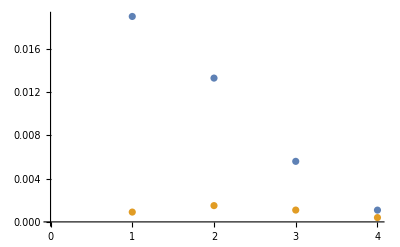

```mathematica
ListPlot[{dataLj,signal0Lj}]
```

```mathematica
s2th = 0.22305;
c2th = 1- s2th;
```

```mathematica
NeventsLj[CB_, CW_]:=backgroundLj+signal0Lj*sigmaVBF[CB,CW]/sigmaVBF[0,1];
```

```mathematica
chi2Lj[CB_, CW_]:=Sum[((dataLj[[i]]-NeventsLj[CB,CW][[i]])/dataUncLj[[i]])^2,{i,0,Length[dataLj]}];
```

```mathematica
chi2minLj=FindMinimum[chi2Lj[CB,CW],{{CB,0},{CW,0}}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.443188,{CB→0.,CW→0.}}

```mathematica
chi2binLj= Table[(((dataLj[[i]]-NeventsLj[CB,CW][[i]])/dataUncLj[[i]])^2-chi2minLj[[1]]/Length[dataLj])/(chi2Lj[CB,CW]-chi2minLj[[1]]),{i,1,Length[dataLj]}];
```

```mathematica
Length[chi2binLj]
```

4

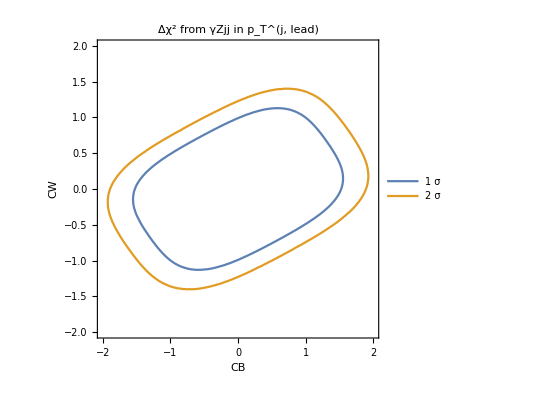

```mathematica
chi2PlotZgammajjpTjlead=ContourPlot[{chi2Lj[CB,CW]-chi2minLj[[1]]==1,chi2Lj[CB,CW]-chi2minLj[[1]]==4},{CB,-2,2},{CW,-2,2} ,FrameLabel->(Style[#,14,Bold]&/@{CB,CW}),PlotLegends->{"1 σ", "2 σ"}, PlotLabel->"Δχ^2 from γZjj in p_T^(j, lead)"]
```

```mathematica
Export["../Figures/chi2_Zgammajj_pTjlead.pdf",chi2PlotZgammajjpTjlead];
```

```mathematica
Solve[chi2Lj[0,CW]-chi2minLj[[1]]==4,CW]
```

{{CW→-1.22765},{CW→-0.946811-0.946811 ⅈ},{CW→-0.946811+0.946811 ⅈ},{CW→0.-1.22765 ⅈ},{CW→0.+1.22765 ⅈ},{CW→0.946811-0.946811 ⅈ},{CW→0.946811+0.946811 ⅈ},{CW→1.22765}}

```mathematica
Solve[chi2Lj[CB,0]-chi2minLj[[1]]==4,CB]
```

{{CB→-1.89248},{CB→-1.45955-1.45955 ⅈ},{CB→-1.45955+1.45955 ⅈ},{CB→0.-1.89248 ⅈ},{CB→0.+1.89248 ⅈ},{CB→1.45955-1.45955 ⅈ},{CB→1.45955+1.45955 ⅈ},{CB→1.89248}}

The individual 2 σ limits are CW = 1.23 and CB = 1.89 for the respective other WC zero .